# Driven systems

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Problem 1: Solve DiffEQ

```mathematica
With[{context="p1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
eqn=y'[t]+2 y[t]==x[t]
drive=x[t]==UnitStep[t]
initial=y[0]==0
```

2 y[t]+y'[t]==x[t]

x[t]==UnitStep[t]

y[0]==0

### Approach 1: Full Mathematica

```mathematica
sol=Simplify@DSolveValue[{eqn, drive, initial},y[t],t]
```

1/2 ⅇ^(-2 t) (-1+ⅇ^(2 t)) UnitStep[t]

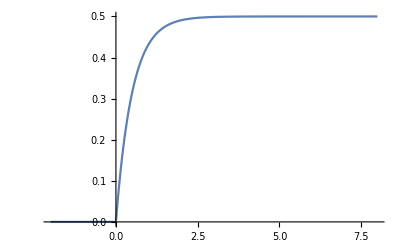

```mathematica
Plot[sol,{t,-2,7.999999999999999}]
```

### Approach 2: Mathematica Laplace

```mathematica
lap=LaplaceTransform[eqn,t,s]
lap2=Solve[lap,LaplaceTransform[y[t],t,s]][[1,1,2]]
lap3=lap2/.{y[0]->0,x[t_]:>UnitStep[t]}
sol2=InverseLaplaceTransform[lap3,s,t]
```

2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]-y[0]==LaplaceTransform[x[t],t,s]

(LaplaceTransform[x[t],t,s]+y[0])/(2+s)

1/(s (2+s))

1/2-ⅇ^(-2 t)/2

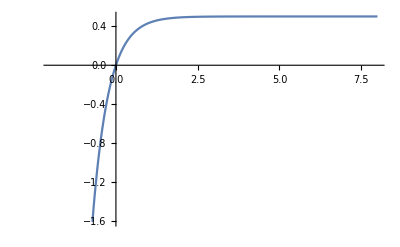

```mathematica
Plot[sol2,{t,-2.,8.}]
```

```mathematica
Simplify[sol==sol2]
```

ⅇ^(-2 t)==1||t≥0

```mathematica
With[{context="p1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Car Suspension

```mathematica
With[{context="p2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Setup

```mathematica
eqn=m y''[t]+c y'[t] + k y[t]==c x'[t]+k x[t]
drive={x[t_]:>UnitStep[t]};
```

k y[t]+c y'[t]+m y''[t]==k x[t]+c x'[t]

```mathematica
initial={y[0]->0,x[0]->0,y'[0]->0};
```

### a) Laplace

```mathematica
lap=LaplaceTransform[eqn,t,s];
(lap2=Solve[lap/.initial/.drive,LaplaceTransform[y[t],t,s]])//TraditionalForm
lap3=lap2[[1,1,2]]
```

{{ℒ_t[y(t)](s)→(c s+k)/(s (c s+k+m s^2))}}

(k+c s)/(s (k+c s+m s^2))

### c) Solve it

##### Setup desired roots

```mathematica
Roots[m s^2+c s+k==0,s]
```

s==(-c-√(c^2-4 k m))/(2 m)||s==(-c+√(c^2-4 k m))/(2 m)

```mathematica
roots={r1==(-c-√(c^2-4 k m))/(2 m),r2==(-c+√(c^2-4 k m))/(2 m)}
```

{r1==(-c-√(c^2-4 k m))/(2 m),r2==(-c+√(c^2-4 k m))/(2 m)}

##### Approach 1: Pure Mathematica

```mathematica
initial2={y[0]==0,y'[0]==0};
```

```mathematica
sol1=Simplify@DSolveValue[{eqn,x[t]==UnitStep[t],initial2},y[t],t]
```

1/(2 √(c^4-4 c^2 k m))ⅇ^(-((c^2+√(c^4-4 c^2 k m)) t)/(2 c m)) (-2 c^2 (-1+ⅇ^((√(c^4-4 c^2 k m) t)/(c m)))-(-c^2 (-1+ⅇ^((√(c^4-4 c^2 k m) t)/(c m)))+(1+ⅇ^((√(c^4-4 c^2 k m) t)/(c m))-2 ⅇ^(((c^2+√(c^4-4 c^2 k m)) t)/(2 c m))) √(c^4-4 c^2 k m)) UnitStep[t])

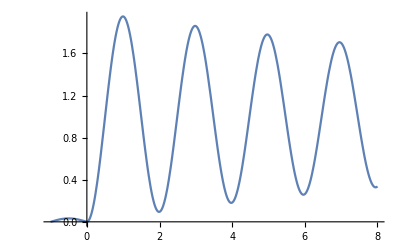

```mathematica
plot1=makePlot[sol1,{m->1000,c->100,k->10000}]
```

##### Approach 2: From Laplace

```mathematica
lap4=(k+c s)/(s (s-Subscript[a, 1]) (s-Subscript[a, 2]));
sol2=InverseLaplaceTransform[lap4,s,t]
```

(ⅇ^(t a_1) (k+c a_1))/(a_1 (a_1-a_2))+k/(a_1 a_2)+(ⅇ^(t a_2) (-k-c a_2))/((a_1-a_2) a_2)

##### Plot it

```mathematica
makePlot[sol_,params_]:=With[{roots={Subscript[a, 1]-> (-c-√(c^2-4 k m))/(2 m),Subscript[a, 2]-> (-c+√(c^2-4 k m))/(2 m)}},
Plot[sol/.roots/.params,{t,-1,8}]]
```

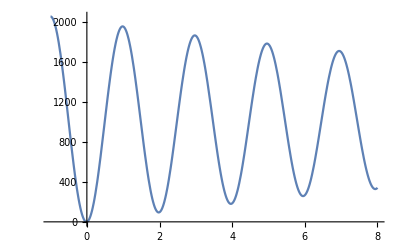

```mathematica
makePlot[sol2,{m->1000,c->100,k->10000}]
```

##### Play with it

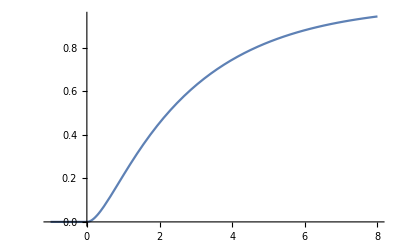

```mathematica
plot2=makePlot[sol1*UnitStep[t],{m->1000,c->3000,k->1000}]
```

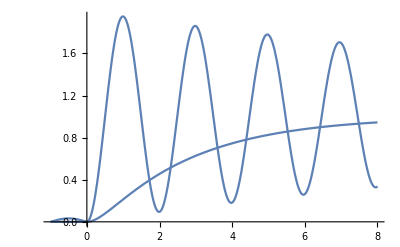

```mathematica
Show[plot1,plot2]
```

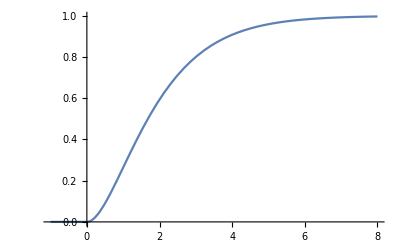

```mathematica
plot3=makePlot[sol1*UnitStep[t],{m->1000,c->2001,k->1000}]
```

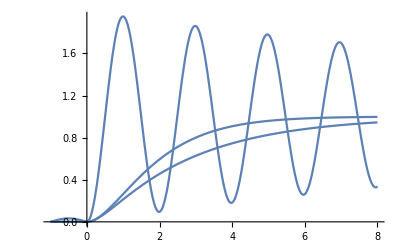

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
With[{context="p2`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Module 3/Driven Systems/Mathematica work.pdf